## CelleratorNetwork-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<xlr8r.m
```

xCellerator 0.90 (2-Nov-2012) loaded Thu 8 Nov 2012 18:39:32
using Mathematica 8.0 for Linux x86 (64-bit) (October 10, 2011) (Version 8., Release 4)
using MathSBML version 2.12

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (2.3.5 (6-Nov-2012)) loaded Thu 8 Nov 2012 18:39:34
using xCellerator 0.90 and XSSA 1204002

Generate 50 random vertices to use a Voronoi Centers

```mathematica
r:=RandomReal[{0,100}]; 
vertices=Table[{r,r}, {10}];
```

Use the Voronoi Centers to generate a tissue with 5 cells using the Bounded-Cell-Voronoi algorithm

```mathematica
w=BoundedCellVoronoi[vertices];
```

Show the tissue and the centers

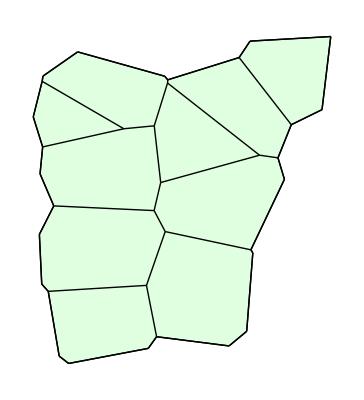

```mathematica
ShowTissue[w]
```

Define the Cellerator Network in a Single Cell

```mathematica
MyReactions = {{Underoverscript[X⟺XP, ZP, Z],MM[K,v,K,v]}, {Underoverscript[Y⟺YP, XP, X],MM[K,v,K,v]},
   {Underoverscript[Z⟺ZP, YP, Y],MM[K,v,K,v]}};
```

Generate the Reactions in the big network

```mathematica
bignet=CelleratorNetwork[w, "Reactions"-> MyReactions, "Diffusion"-> {{X,DX},{Y,DY},{Z,DZ}}];
```

10 Cells.

6 internal reactions in each cell.

60 intracellular reactions.

102 diffusion reactions.

162 total reactions.

```mathematica
bignet
```

{{(X[1]⟹XP[1])^Z[1],MM[K,v]},{(XP[1]⟹X[1])^ZP[1],MM[K,v]},{(Y[1]⟹YP[1])^X[1],MM[K,v]},{(YP[1]⟹Y[1])^XP[1],MM[K,v]},{(Z[1]⟹ZP[1])^Y[1],MM[K,v]},{(ZP[1]⟹Z[1])^YP[1],MM[K,v]},{(X[2]⟹XP[2])^Z[2],MM[K,v]},{(XP[2]⟹X[2])^ZP[2],MM[K,v]},{(Y[2]⟹YP[2])^X[2],MM[K,v]},{(YP[2]⟹Y[2])^XP[2],MM[K,v]},{(Z[2]⟹ZP[2])^Y[2],MM[K,v]},{(ZP[2]⟹Z[2])^YP[2],MM[K,v]},{(X[3]⟹XP[3])^Z[3],MM[K,v]},{(XP[3]⟹X[3])^ZP[3],MM[K,v]},{(Y[3]⟹YP[3])^X[3],MM[K,v]},{(YP[3]⟹Y[3])^XP[3],MM[K,v]},{(Z[3]⟹ZP[3])^Y[3],MM[K,v]},{(ZP[3]⟹Z[3])^YP[3],MM[K,v]},{(X[4]⟹XP[4])^Z[4],MM[K,v]},{(XP[4]⟹X[4])^ZP[4],MM[K,v]},{(Y[4]⟹YP[4])^X[4],MM[K,v]},{(YP[4]⟹Y[4])^XP[4],MM[K,v]},{(Z[4]⟹ZP[4])^Y[4],MM[K,v]},{(ZP[4]⟹Z[4])^YP[4],MM[K,v]},{(X[5]⟹XP[5])^Z[5],MM[K,v]},{(XP[5]⟹X[5])^ZP[5],MM[K,v]},{(Y[5]⟹YP[5])^X[5],MM[K,v]},{(YP[5]⟹Y[5])^XP[5],MM[K,v]},{(Z[5]⟹ZP[5])^Y[5],MM[K,v]},{(ZP[5]⟹Z[5])^YP[5],MM[K,v]},{(X[6]⟹XP[6])^Z[6],MM[K,v]},{(XP[6]⟹X[6])^ZP[6],MM[K,v]},{(Y[6]⟹YP[6])^X[6],MM[K,v]},{(YP[6]⟹Y[6])^XP[6],MM[K,v]},{(Z[6]⟹ZP[6])^Y[6],MM[K,v]},{(ZP[6]⟹Z[6])^YP[6],MM[K,v]},{(X[7]⟹XP[7])^Z[7],MM[K,v]},{(XP[7]⟹X[7])^ZP[7],MM[K,v]},{(Y[7]⟹YP[7])^X[7],MM[K,v]},{(YP[7]⟹Y[7])^XP[7],MM[K,v]},{(Z[7]⟹ZP[7])^Y[7],MM[K,v]},{(ZP[7]⟹Z[7])^YP[7],MM[K,v]},{(X[8]⟹XP[8])^Z[8],MM[K,v]},{(XP[8]⟹X[8])^ZP[8],MM[K,v]},{(Y[8]⟹YP[8])^X[8],MM[K,v]},{(YP[8]⟹Y[8])^XP[8],MM[K,v]},{(Z[8]⟹ZP[8])^Y[8],MM[K,v]},{(ZP[8]⟹Z[8])^YP[8],MM[K,v]},{(X[9]⟹XP[9])^Z[9],MM[K,v]},{(XP[9]⟹X[9])^ZP[9],MM[K,v]},{(Y[9]⟹YP[9])^X[9],MM[K,v]},{(YP[9]⟹Y[9])^XP[9],MM[K,v]},{(Z[9]⟹ZP[9])^Y[9],MM[K,v]},{(ZP[9]⟹Z[9])^YP[9],MM[K,v]},{(X[10]⟹XP[10])^Z[10],MM[K,v]},{(XP[10]⟹X[10])^ZP[10],MM[K,v]},{(Y[10]⟹YP[10])^X[10],MM[K,v]},{(YP[10]⟹Y[10])^XP[10],MM[K,v]},{(Z[10]⟹ZP[10])^Y[10],MM[K,v]},{(ZP[10]⟹Z[10])^YP[10],MM[K,v]},{X[1]⇄∅,0.041826 DX,0.041826 DX X[9][t]},{X[2]⇄∅,0.0261927 DX,0.0261927 DX X[4][t]},{X[2]⇄∅,0.0316189 DX,0.0316189 DX X[5][t]},{X[2]⇄∅,0.0179409 DX,0.0179409 DX X[6][t]},{X[2]⇄∅,0.0096094 DX,0.0096094 DX X[8][t]},{X[2]⇄∅,0.00906002 DX,0.00906002 DX X[10][t]},{X[3]⇄∅,0.0386958 DX,0.0386958 DX X[5][t]},{X[3]⇄∅,0.0205405 DX,0.0205405 DX X[7][t]},{X[4]⇄∅,0.073398 DX,0.073398 DX X[2][t]},{X[4]⇄∅,0.0833194 DX,0.0833194 DX X[8][t]},{X[5]⇄∅,0.0287939 DX,0.0287939 DX X[2][t]},{X[5]⇄∅,0.0282147 DX,0.0282147 DX X[3][t]},{X[5]⇄∅,0.0163107 DX,0.0163107 DX X[7][t]},{X[5]⇄∅,0.00680324 DX,0.00680324 DX X[10][t]},{X[6]⇄∅,0.0279545 DX,0.0279545 DX X[2][t]},{X[6]⇄∅,0.0219534 DX,0.0219534 DX X[8][t]},{X[6]⇄∅,0.0573264 DX,0.0573264 DX X[9][t]},{X[6]⇄∅,0.0503036 DX,0.0503036 DX X[10][t]},{X[7]⇄∅,0.0141202 DX,0.0141202 DX X[3][t]},{X[7]⇄∅,0.0153777 DX,0.0153777 DX X[5][t]},{X[7]⇄∅,0.0236785 DX,0.0236785 DX X[10][t]},{X[8]⇄∅,0.013883 DX,0.013883 DX X[2][t]},{X[8]⇄∅,0.0429565 DX,0.0429565 DX X[4][t]},{X[8]⇄∅,0.0203555 DX,0.0203555 DX X[6][t]},{X[8]⇄∅,0.00145471 DX,0.00145471 DX X[9][t]},{X[9]⇄∅,0.036781 DX,0.036781 DX X[1][t]},{X[9]⇄∅,0.0505945 DX,0.0505945 DX X[6][t]},{X[9]⇄∅,0.00138467 DX,0.00138467 DX X[8][t]},{X[9]⇄∅,0.0080588 DX,0.0080588 DX X[10][t]},{X[10]⇄∅,0.00906581 DX,0.00906581 DX X[2][t]},{X[10]⇄∅,0.00747549 DX,0.00747549 DX X[5][t]},{X[10]⇄∅,0.032305 DX,0.032305 DX X[6][t]},{X[10]⇄∅,0.0275969 DX,0.0275969 DX X[7][t]},{X[10]⇄∅,0.00586398 DX,0.00586398 DX X[9][t]},{Y[1]⇄∅,0.041826 DY,0.041826 DY Y[9][t]},{Y[2]⇄∅,0.0261927 DY,0.0261927 DY Y[4][t]},{Y[2]⇄∅,0.0316189 DY,0.0316189 DY Y[5][t]},{Y[2]⇄∅,0.0179409 DY,0.0179409 DY Y[6][t]},{Y[2]⇄∅,0.0096094 DY,0.0096094 DY Y[8][t]},{Y[2]⇄∅,0.00906002 DY,0.00906002 DY Y[10][t]},{Y[3]⇄∅,0.0386958 DY,0.0386958 DY Y[5][t]},{Y[3]⇄∅,0.0205405 DY,0.0205405 DY Y[7][t]},{Y[4]⇄∅,0.073398 DY,0.073398 DY Y[2][t]},{Y[4]⇄∅,0.0833194 DY,0.0833194 DY Y[8][t]},{Y[5]⇄∅,0.0287939 DY,0.0287939 DY Y[2][t]},{Y[5]⇄∅,0.0282147 DY,0.0282147 DY Y[3][t]},{Y[5]⇄∅,0.0163107 DY,0.0163107 DY Y[7][t]},{Y[5]⇄∅,0.00680324 DY,0.00680324 DY Y[10][t]},{Y[6]⇄∅,0.0279545 DY,0.0279545 DY Y[2][t]},{Y[6]⇄∅,0.0219534 DY,0.0219534 DY Y[8][t]},{Y[6]⇄∅,0.0573264 DY,0.0573264 DY Y[9][t]},{Y[6]⇄∅,0.0503036 DY,0.0503036 DY Y[10][t]},{Y[7]⇄∅,0.0141202 DY,0.0141202 DY Y[3][t]},{Y[7]⇄∅,0.0153777 DY,0.0153777 DY Y[5][t]},{Y[7]⇄∅,0.0236785 DY,0.0236785 DY Y[10][t]},{Y[8]⇄∅,0.013883 DY,0.013883 DY Y[2][t]},{Y[8]⇄∅,0.0429565 DY,0.0429565 DY Y[4][t]},{Y[8]⇄∅,0.0203555 DY,0.0203555 DY Y[6][t]},{Y[8]⇄∅,0.00145471 DY,0.00145471 DY Y[9][t]},{Y[9]⇄∅,0.036781 DY,0.036781 DY Y[1][t]},{Y[9]⇄∅,0.0505945 DY,0.0505945 DY Y[6][t]},{Y[9]⇄∅,0.00138467 DY,0.00138467 DY Y[8][t]},{Y[9]⇄∅,0.0080588 DY,0.0080588 DY Y[10][t]},{Y[10]⇄∅,0.00906581 DY,0.00906581 DY Y[2][t]},{Y[10]⇄∅,0.00747549 DY,0.00747549 DY Y[5][t]},{Y[10]⇄∅,0.032305 DY,0.032305 DY Y[6][t]},{Y[10]⇄∅,0.0275969 DY,0.0275969 DY Y[7][t]},{Y[10]⇄∅,0.00586398 DY,0.00586398 DY Y[9][t]},{Z[1]⇄∅,0.041826 DZ,0.041826 DZ Z[9][t]},{Z[2]⇄∅,0.0261927 DZ,0.0261927 DZ Z[4][t]},{Z[2]⇄∅,0.0316189 DZ,0.0316189 DZ Z[5][t]},{Z[2]⇄∅,0.0179409 DZ,0.0179409 DZ Z[6][t]},{Z[2]⇄∅,0.0096094 DZ,0.0096094 DZ Z[8][t]},{Z[2]⇄∅,0.00906002 DZ,0.00906002 DZ Z[10][t]},{Z[3]⇄∅,0.0386958 DZ,0.0386958 DZ Z[5][t]},{Z[3]⇄∅,0.0205405 DZ,0.0205405 DZ Z[7][t]},{Z[4]⇄∅,0.073398 DZ,0.073398 DZ Z[2][t]},{Z[4]⇄∅,0.0833194 DZ,0.0833194 DZ Z[8][t]},{Z[5]⇄∅,0.0287939 DZ,0.0287939 DZ Z[2][t]},{Z[5]⇄∅,0.0282147 DZ,0.0282147 DZ Z[3][t]},{Z[5]⇄∅,0.0163107 DZ,0.0163107 DZ Z[7][t]},{Z[5]⇄∅,0.00680324 DZ,0.00680324 DZ Z[10][t]},{Z[6]⇄∅,0.0279545 DZ,0.0279545 DZ Z[2][t]},{Z[6]⇄∅,0.0219534 DZ,0.0219534 DZ Z[8][t]},{Z[6]⇄∅,0.0573264 DZ,0.0573264 DZ Z[9][t]},{Z[6]⇄∅,0.0503036 DZ,0.0503036 DZ Z[10][t]},{Z[7]⇄∅,0.0141202 DZ,0.0141202 DZ Z[3][t]},{Z[7]⇄∅,0.0153777 DZ,0.0153777 DZ Z[5][t]},{Z[7]⇄∅,0.0236785 DZ,0.0236785 DZ Z[10][t]},{Z[8]⇄∅,0.013883 DZ,0.013883 DZ Z[2][t]},{Z[8]⇄∅,0.0429565 DZ,0.0429565 DZ Z[4][t]},{Z[8]⇄∅,0.0203555 DZ,0.0203555 DZ Z[6][t]},{Z[8]⇄∅,0.00145471 DZ,0.00145471 DZ Z[9][t]},{Z[9]⇄∅,0.036781 DZ,0.036781 DZ Z[1][t]},{Z[9]⇄∅,0.0505945 DZ,0.0505945 DZ Z[6][t]},{Z[9]⇄∅,0.00138467 DZ,0.00138467 DZ Z[8][t]},{Z[9]⇄∅,0.0080588 DZ,0.0080588 DZ Z[10][t]},{Z[10]⇄∅,0.00906581 DZ,0.00906581 DZ Z[2][t]},{Z[10]⇄∅,0.00747549 DZ,0.00747549 DZ Z[5][t]},{Z[10]⇄∅,0.032305 DZ,0.032305 DZ Z[6][t]},{Z[10]⇄∅,0.0275969 DZ,0.0275969 DZ Z[7][t]},{Z[10]⇄∅,0.00586398 DZ,0.00586398 DZ Z[9][t]}}

Define some random initial conditions

```mathematica
r:=RandomReal[{0,2}]; 
MyIC=Sort[Flatten[{X[#]-> r, Y[#]-> r, Z[#]-> r, XP[#]-> r, YP[#]-> r, ZP[#]-> r}&/@Range[10]]]
```

{X[1]→1.69353,X[2]→0.990878,X[3]→1.65076,X[4]→1.20944,X[5]→1.05105,X[6]→1.31972,X[7]→1.82029,X[8]→1.04756,X[9]→1.5223,X[10]→0.0662658,XP[1]→0.986346,XP[2]→1.4632,XP[3]→0.591909,XP[4]→1.7166,XP[5]→0.126179,XP[6]→0.749341,XP[7]→0.160975,XP[8]→1.50026,XP[9]→0.975218,XP[10]→1.47198,Y[1]→1.6708,Y[2]→0.66441,Y[3]→0.708521,Y[4]→1.28033,Y[5]→0.0088752,Y[6]→1.13567,Y[7]→1.25801,Y[8]→0.869992,Y[9]→0.582596,Y[10]→0.99188,YP[1]→0.8125,YP[2]→0.838905,YP[3]→1.37974,YP[4]→0.498793,YP[5]→0.402601,YP[6]→0.936904,YP[7]→0.239667,YP[8]→0.34808,YP[9]→1.88374,YP[10]→0.285127,Z[1]→1.88858,Z[2]→1.81043,Z[3]→1.29646,Z[4]→0.352388,Z[5]→1.82682,Z[6]→0.101631,Z[7]→0.131721,Z[8]→0.909327,Z[9]→1.5168,Z[10]→0.653595,ZP[1]→1.80117,ZP[2]→1.29781,ZP[3]→0.589108,ZP[4]→0.0833847,ZP[5]→1.2727,ZP[6]→1.31133,ZP[7]→0.04038,ZP[8]→1.06999,ZP[9]→1.49549,ZP[10]→1.59961}

Define the Paraemters and run a single simulation

```mathematica
MyParameters = {v -> 1, K -> .5, DX-> 13, DY-> 15, DZ-> 11};
```

```mathematica
mysim = run[bignet, {0, 25}, rates->MyParameters, initialConditions-> MyIC];
```

Plot the results

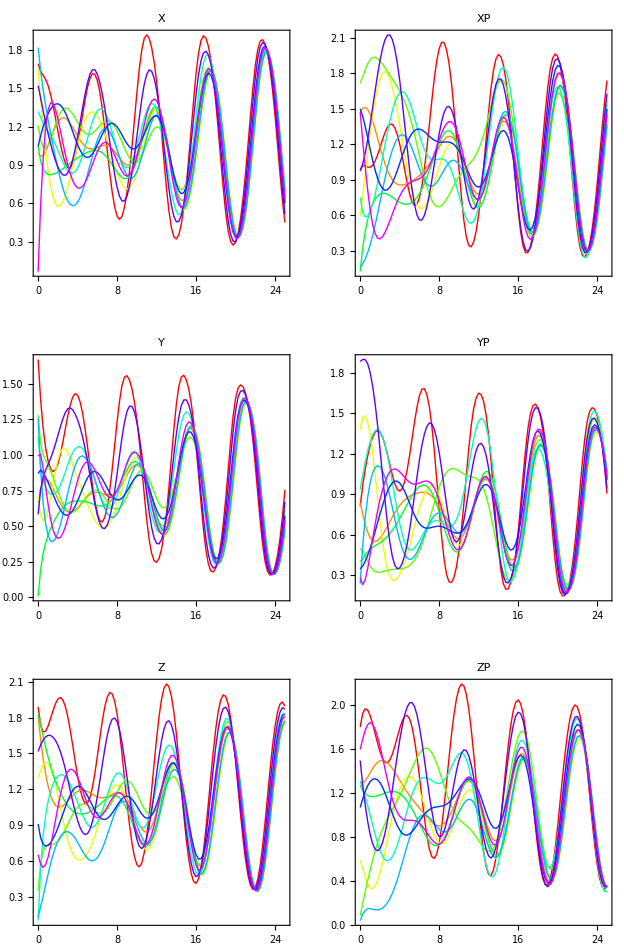

```mathematica
GraphicsGrid[Partition[SimPlot[mysim],2]]
```